```mathematica
(** Static case figure **)
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

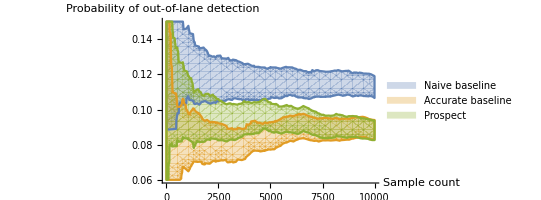

```mathematica
legendFontSize = 24; 
labelFontSize = 18; 
rpStat = RegionPlot[{
IntervalMemberQ[outDetIntsPPnaive[[ Ceiling@x ]], y], 
IntervalMemberQ[outDetIntsPPaccurate[[ Ceiling@x ]], y],
IntervalMemberQ[outDetIntsOurs[[ Ceiling@x ]], y]},
{x,1,statLen},{y,0.06,0.15},
PlotLegends->Placed[{Style[" Naive baseline", legendFontSize, Darker@Gray],Style[" Accurate baseline", legendFontSize, Darker@Gray],Style[" Prospect", legendFontSize, Darker@Gray]}, {0.75,0.85}],
(*FrameLabel->{"x","y"},RotateLabel->False,*)
Frame->None, Axes->True, AxesLabel->{"    Sample count", "                     Probability of out-of-lane detection"}, LabelStyle->{FontSize->labelFontSize, FontColor->Darker@Gray},
(*ImageSize->{1500,600},*)
AspectRatio->0.5
(*PlotRange->{{1000,10000}, {0.05, 0.15}}]*)
]
```

```mathematica
(** Time-invariant case figure **)
```

```mathematica
RegionPlot[{
IntervalMemberQ[pingFlipIntsPPnaive[[ Ceiling@x ]], y],
IntervalMemberQ[pingFlipIntsPPaccurate[[ Ceiling@x ]], y],
IntervalMemberQ[pingFlipIntsOurs[[ Ceiling@x ]], y]},
{x,1,invLen},{y,0.45,0.73},
PlotLegends->Placed[{Style[" Naive baseline", legendFontSize, Darker@Gray],Style[" Accurate baseline", legendFontSize, Darker@Gray],Style[" Prospect", legendFontSize, Darker@Gray]}, {0.5,1}],
Frame->None, Axes->True, AxesLabel->{"    Sample count", "                     Probability of ping not changing"}, LabelStyle->{FontSize->labelFontSize, FontColor->Darker@Gray},
AspectRatio->0.75
]
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

-Graphics-

```mathematica
(** Time-variant case figure **)
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

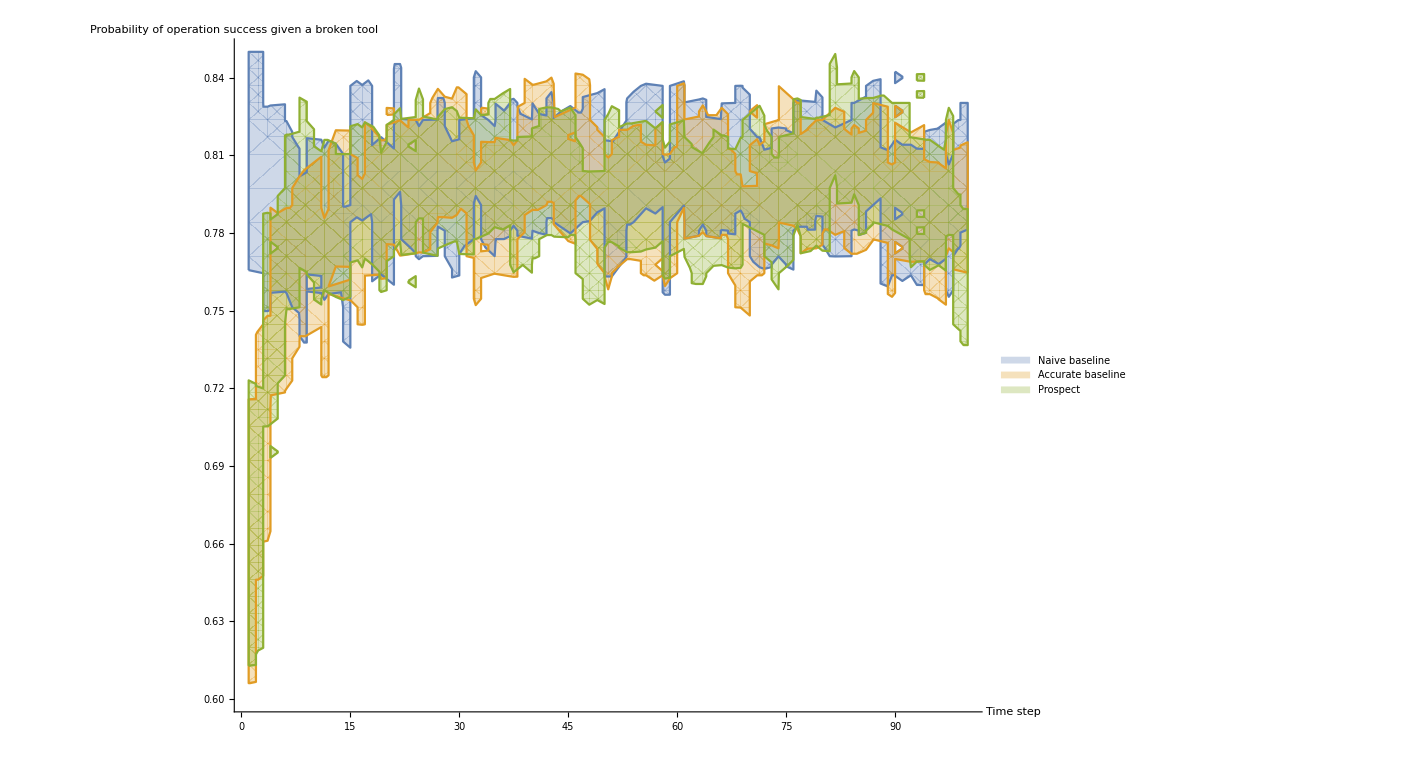

```mathematica
RegionPlot[{
IntervalMemberQ[condOkToolBrokeIntNaive[[ Ceiling@x ]], y], 
IntervalMemberQ[condOkToolBrokeIntAccurate[[ Ceiling@x ]], y],
IntervalMemberQ[condOkToolBrokeIntOurs[[ Ceiling@x ]], y]},
{x,1,varRunLen},{y,0.6,0.85},
PlotLegends->Placed[{Style[" Naive baseline", legendFontSize, Darker@Gray],Style[" Accurate baseline", legendFontSize, Darker@Gray],Style[" Prospect", legendFontSize, Darker@Gray]}, {0.84,0.27}],
Frame->None, Axes->True, AxesLabel->{"  Time step", "Probability of operation success given a broken tool"}, LabelStyle->{FontSize->labelFontSize, FontColor->Darker@Gray},
AspectRatio->0.75
]
```